```mathematica
ElectronGun[t_]:=UnitBox[36000000t+0.5] (*1 Pixel = 36 MHz*)
P22R[t_]:= Piecewise[{{4 ⅇ^(-2 π t *360)+1.75 ⅇ^(-2  π t 1600)+2 ⅇ^(-2 π t 8000)+2.25 ⅇ^(-2 π t 25000)+15 ⅇ^(-2 π t 700000)+29 ⅇ^(-2 π t 7000000), t>=0}, {0, t<0}}]
P22G[t_]:= Piecewise[{{210*10^-6*(t+5.5*10^-6)^-1.1+37 ⅇ^(-2 π t *150000)+100 ⅇ^(-2  π t 700000)+90 ⅇ^(-2 π t 5000000), t>=0}, {0, t<0}}]
P22B[t_]:= Piecewise[{{190*10^-6*(t+5*10^-6)^-1.11+75 ⅇ^(-2 π t *100000)+1000 ⅇ^(-2 π t 1100000)+1100 ⅇ^(-2 π t 4000000), t>=0}, {0, t<0}}]
P22Rn[t_]:=1/54 P22R[t] (*normalized*)
P22Gn[t_]:=1/355.1800203774875 P22G[t] (*normalized*)
P22Bn[t_]:=1/2320.5113587732703 P22B[t] (*normalized*)

Pixel[t_]:=UnitBox[16*10^6 t+0.5] (*Subscript[f, p] = 16MHz, ignoring rise time, normalized*)
PixelLine[t_]:=Pixel[320^-1 t] (*640x320 display*)

BluR[t_]:=1/(3.81649×10^-8)Convolve[P22Rn[dt],Pixel[dt],dt,t]
BluG[t_]:=1/(5.105723739797729*^-8)Convolve[P22Gn[dt],Pixel[dt],dt,t]
BluB[t_]:=1/(4.2684331713668844*^-8)Convolve[P22Bn[dt],Pixel[dt],dt,t]
```

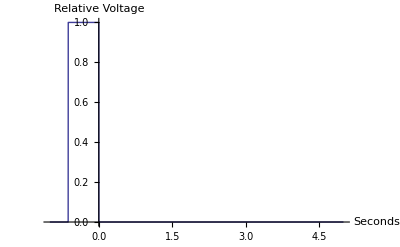

```mathematica
Plot[Pixel[t],{t,-10^-7,5*10^-7},AxesLabel->{"Seconds","Relative Voltage"}]
```

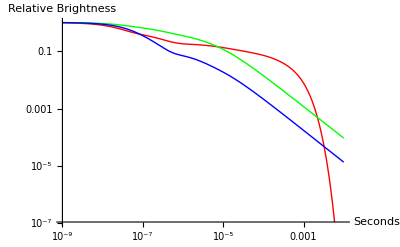

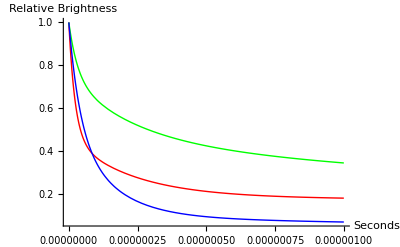

```mathematica
(*Impulse responses*)
LogLogPlot[{P22Rn[t],P22Gn[t],P22Bn[t]},{t,10^-9,10^-2},PlotStyle->{Red,Green,Blue},AxesLabel->{"Seconds","Relative Brightness"}]
Plot[{P22Rn[t],P22Gn[t],P22Bn[t]},{t,0,10^-6},PlotRange->Full,PlotStyle->{Red,Green,Blue},AxesLabel->{"Seconds","Relative Brightness"}]
```

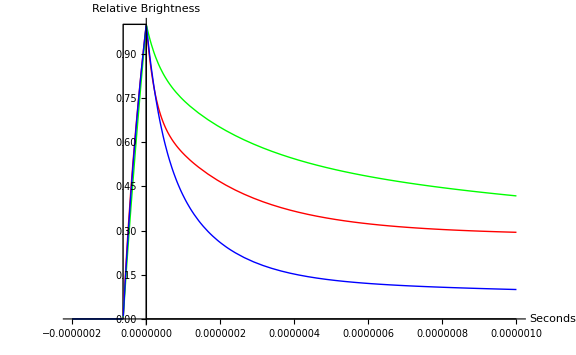

```mathematica
(* Pixel responses. Saved crazy anaythical convolution results below for faster plots only *)
Plot[{Pixel[t],BluRn[t],{{BluGn[t], BluBn[t]}}},{t,-2*10^-7,10^-6},PlotRange->Full,PlotStyle->{Black,Red,Green,Blue},ImageSize->Large,AxesLabel->{"Seconds","Relative Brightness"}]
```

```mathematica
BluRn[t_]:=1/(54*3.81649×10^-8) (Piecewise[{{6.315672344916482*^-10 (3.167749*^6-2.8*^6 ⅇ^(0.04523893421169302 (-0.003125-50000. t))-275625. ⅇ^(0.20106192982974677 (-0.003125-50000. t))-63000. ⅇ^(1.0053096491487339 (-0.003125-50000. t))-22680. ⅇ^(3.141592653589793 (-0.003125-50000. t))-5400. ⅇ^(87.96459430051421 (-0.003125-50000. t))-1044. ⅇ^(879.645943005142 (-0.003125-50000. t))), -6.25*^-8<t≤0.}, {6.315672344916482*^-10 ⅇ^(-2.748893571891069-4.39822971502571*^7 t) (15268.848704108585-2.8*^6 ⅇ^(2.7487522002216576+4.398003520354652*^7 t)+2.8*^6 ⅇ^(2.748893571891069+4.398003520354652*^7 t)-275625. ⅇ^(2.748893571891069+3.141592653589793 (-0.0002-3200. t)+4.39822971502571*^7 t)+275625. ⅇ^(2.749521890421787+3.141592653589793 (-0.0002-3200. t)+4.39822971502571*^7 t)-63000. ⅇ^(2.748893571891069+15.707963267948966 (-0.0002-3200. t)+4.39822971502571*^7 t)+63000. ⅇ^(2.752035164544659+15.707963267948966 (-0.0002-3200. t)+4.39822971502571*^7 t)-22680. ⅇ^(2.748893571891069+49.087385212340514 (-0.0002-3200. t)+4.39822971502571*^7 t)+22680. ⅇ^(2.758711048933537+49.087385212340514 (-0.0002-3200. t)+4.39822971502571*^7 t)-5400. ⅇ^(2.748893571891069+1374.4467859455344 (-0.0002-3200. t)+4.39822971502571*^7 t)+5400. ⅇ^(3.023782929080176+1374.4467859455344 (-0.0002-3200. t)+4.39822971502571*^7 t)), t>0.}, {0., True}}])
BluGn[t_]:=0.002815473682717834/(5.105723739797729*^-8) (Piecewise[{{1/((89.+1.6*^7 t)^(1/10))1.377964875254505*^-9 ⅇ^(-1.9634954084936207-3.1415926535897933*^7 t) (-8.005586337212232*^6 ⅇ^(1.9634954084936207+3.1415926535897933*^7 t)-2079. (89.+1.6*^7 t)^(1/10)+5.163237958559056*^6 ⅇ^(1.9634954084936207+3.1415926535897933*^7 t) (89.+1.6*^7 t)^(1/10)-28490. ⅇ^(1.9634954084936207+3.141592653589793 (-0.01875-300000. t)+3.1415926535897933*^7 t) (89.+1.6*^7 t)^(1/10)-16500. ⅇ^(1.9634954084936207+14.660765716752369 (-0.01875-300000. t)+3.1415926535897933*^7 t) (89.+1.6*^7 t)^(1/10)), -6.25*^-8<t≤0.}, {1/((11.+2.*^6 t)^(1/10) (89.+1.6*^7 t)^(1/10))1.5157613627799557*^-8 ⅇ^(-1.9634954084936207-3.1415926535897933*^7 t) (-727780.5761102029 ⅇ^(1.9634954084936207+3.1415926535897933*^7 t) (11.+2.*^6 t)^(1/10)+591141.5169670339 ⅇ^(1.9634954084936207+3.1415926535897933*^7 t) (89.+1.6*^7 t)^(1/10)+1157.4710657784979 (11.+2.*^6 t)^(1/10) (89.+1.6*^7 t)^(1/10)-1500. ⅇ^(1.6886060513045138+2.701769682087222*^7 t) (11.+2.*^6 t)^(1/10) (89.+1.6*^7 t)^(1/10)+1500. ⅇ^(1.9634954084936207+2.701769682087222*^7 t) (11.+2.*^6 t)^(1/10) (89.+1.6*^7 t)^(1/10)+2590. ⅇ^(1.9634954084936207+3.0473448739820994*^7 t) (11.+2.*^6 t)^(1/10) (89.+1.6*^7 t)^(1/10)-2590. ⅇ^(1.9634954084936207+3.141592653589793 (-0.01875-300000. t)+3.1415926535897933*^7 t) (11.+2.*^6 t)^(1/10) (89.+1.6*^7 t)^(1/10)), t>0.}, {0., True}}])
BluBn[t_]:=0.00043093949797713823/(4.2684331713668844*^-8)(Piecewise[{{1/((81.+1.6*^7 t)^(11/100))3.617157797543076*^-7 (-29610.562578067806+19136.49662943895 (81.+1.6*^7 t)^(11/100)-330. ⅇ^(3.141592653589793 (-0.0125-200000. t)) (81.+1.6*^7 t)^(11/100)-400. ⅇ^(34.55751918948772 (-0.0125-200000. t)) (81.+1.6*^7 t)^(11/100)-121. ⅇ^(125.66370614359172 (-0.0125-200000. t)) (81.+1.6*^7 t)^(11/100)), -6.25*^-8<t≤0.}, {1/((1.+200000. t)^(11/100) (81.+1.6*^7 t)^(11/100))3.617157797543076*^-7 ⅇ^(-1.5707963267948966-2.5132741228718344*^7 t) (-29610.562578067806 ⅇ^(1.5707963267948966+2.5132741228718344*^7 t) (1.+200000. t)^(11/100)+18285.49662943895 ⅇ^(1.5707963267948966+2.5132741228718344*^7 t) (81.+1.6*^7 t)^(11/100)+461.06776309680754 (1.+200000. t)^(11/100) (81.+1.6*^7 t)^(11/100)-400. ⅇ^(1.1388273369263+1.82212373908208*^7 t) (1.+200000. t)^(11/100) (81.+1.6*^7 t)^(11/100)+400. ⅇ^(1.5707963267948966+1.82212373908208*^7 t) (1.+200000. t)^(11/100) (81.+1.6*^7 t)^(11/100)+330. ⅇ^(1.5707963267948966+2.4504422698000386*^7 t) (1.+200000. t)^(11/100) (81.+1.6*^7 t)^(11/100)-330. ⅇ^(1.5707963267948966+3.141592653589793 (-0.0125-200000. t)+2.5132741228718344*^7 t) (1.+200000. t)^(11/100) (81.+1.6*^7 t)^(11/100)), t>0.}, {0., True}}])
```